{6912,1}

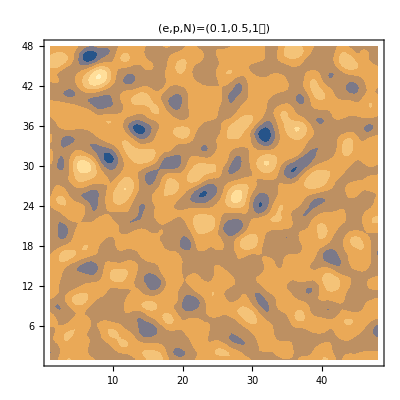

{48,48,3}

```mathematica
Needs["VectorFieldPlots`"];
SetDirectory[NotebookDirectory[]];
p=ReadList["eigen16.txt",Number,RecordLists-> True];
Dimensions[p]
L=48;
p2=Table[{p[[L*3*(i-1)+3*(j-1)+1,1]],p[[L*3*(i-1)+3*(j-1)+2,1]],p[[L*3*(i-1)+3*(j-1)+3,1]]},{i,1,L,1},{j,1,L,1}];
edge=1;
ListContourPlot[p2[[All,All,3]],PlotLabel->Style["(e,p,N)=(0.1,0.5,1만)",FontSize->20],FrameTicksStyle->Directive[FontOpacity->0,FontSize->0], ContourStyle->None,InterpolationOrder->2]
Dimensions[p2]
```